## Day 1

## Problem 1

### Part 1

```mathematica
ψ1[x]:=ⅇ^(-x^2/4)
ψ2[x]:=x ⅇ^(-x^2/8)
ψ3[x]:=ψ1[x]+ψ2[x]
A1=1/√Integrate[ψ1[x]^2,{x,-Infinity,Infinity}]
A2=1/√Integrate[ψ2[x]^2,{x,-Infinity,Infinity}]
A3=1/√Integrate[ψ3[x]^2,{x,-Infinity, Infinity}]
```

```mathematica
1/(2 π)^(1/4)(*This is the normalization constant for ψ1*)
```

```mathematica
1/(2 π^(1/4))(*This is the normalization constant for ψ2*)
```

```mathematica
1/(√(4+√2) π^(1/4))(*This is the normalization constant for ψ3*)
```

### Part 2

```mathematica
NIntegrate[A1 ψ1[x],{x,0,1}]
Integrate[A2 ψ2[x],{x,0,1}]
NIntegrate[A3 ψ3[x],{x,0,1}]
```

```mathematica
0.5827074909358458 (*This is the probability of finding the particle between 0 and 1 for ψ1*)
```

```mathematica
(2-2/ⅇ^(1/8))/π^(1/4)(*This is the probability of finding the particle between 0 and 1 for ψ1*)
```

```mathematica
0.44953472858946775(*This is the probability of finding the particle between 0 and 1 for ψ1*)
```

### Part 3

```mathematica
NIntegrate[A1 ψ1[x] + A2 ψ2[x],{x,-1,1}]
NIntegrate[A3 ψ3[x],{x,-1,1}]
```

1.16541

0.595622

The probability of finding a particle between -1 and 1 is not the same for ψ1 + ψ2  as for ψ3

## Problem 2

### Part 1

```mathematica
ψ[x]:=ⅇ^(-x^2/100)ⅇ^(ⅈ 0.3 x)
A=1/√Integrate[ψ[x] Conjugate[ψ[x]],{x,-Infinity,Infinity}]
```

```mathematica
1/(√5 (2 π)^(1/4))(*This is the normalization constant of ψ*)
```

### Part 2

```mathematica
expx=Integrate[x A^2 ψ[x] Conjugate[ψ[x]],{x,-Infinity,Infinity}]
```

```mathematica
0(*This is the expectation value of <x>*)
```

### Part 3

```mathematica
expxsq=Integrate[x^2 A^2 ψ[x] Conjugate[ψ[x]],{x,-Infinity,Infinity}]
```

```mathematica
25(*This is the expectation value of <x^2>*)
```

### Part 4

```mathematica
expxsq-expx^2
```

```mathematica
25(*This is the variance of ψ*)
```

## Problem 3

### Part 1

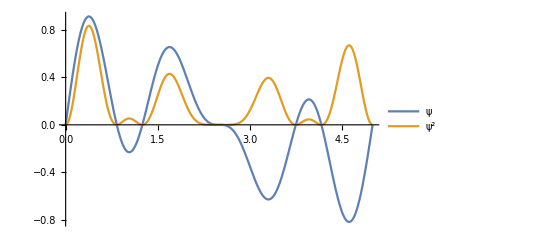

```mathematica
ψnew[x]:=1/(√6.84592)Cos[x/10](Sin[(2 π x)/5]+Sin[(6 π x)/5]+Sin[(8π x)/5])
Plot[{ψnew[x],ψnew[x]^2},{x,0,5},PlotLegends->{"ψ","ψ^2"}]
```

### Part 2

```mathematica
Integrate[ψnew[x]^2,{x,0,5}]
```

```mathematica
0.9999997488235263 (*This means that it is normalized, beyond numerical error *)
```

### Part 3

```mathematica
expxnew=NIntegrate[x ψnew[x]^2,{x,0,5}]
```

```mathematica
2.3465695968040268 (*This is the expectation value of <x>*)
```

### Part 4

```mathematica
expxsqnew=NIntegrate[x^2 ψnew[x]^2,{x,0,5}]
```

```mathematica
8.453339501150799(*This is the expectation value of <x^2>*)
```

### Part 5

```mathematica
expxsqnew-expxnew^2
```

```mathematica
2.9469506285057863(*This is the variance of ψ*)
```